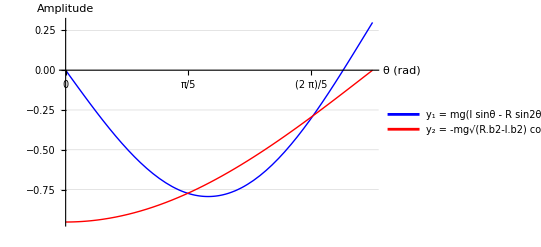

```mathematica
(*定义参数*)R=1; (*设定 R=1 作为单位长度*)
l=0.3 R;
(*定义修正后的公式*)
y1[θ_]:= (l Sin[θ]-R Sin[2 θ])
y2[θ_]:=- Sqrt[R^2-l^2] Cos[θ]

(*绘制图像*)
Plot[{y1[θ],y2[θ]},{θ,0,Pi/2},PlotStyle->{{Thick,Blue},{Thick,Red}},PlotLegends->{"y₁ = mg(l sinθ - R sin2θ)","y₂ = -mg√(R.b2-l.b2) cosθ"},AxesLabel->{"θ (rad)","Amplitude"},PlotRange->All,GridLines->Automatic,Ticks->{Subdivide[0,Pi/2,5],Automatic}]
```